# CUSUMMaxRandomnessTest

Conducts a cumulative sum–based randomness test that creates a test statistic from the maximum value that a cumulative sums random walk achieves.

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

```mathematica
CUSUMmaxstat[seq_]:=Max@Abs@Accumulate[2 seq-1];
Φ[x_]=CDF[NormalDistribution[],x];
CUSUMmaxpval=Function[{z,n},1.-Sum[Φ[(z(4k+1))/(√n)]-Φ[(z(4k-1))/(√n)],{k,Floor[(-n/z+1)/4],(n/z-1)/4,1}]+Sum[Φ[(z(4k+3))/(√n)]-Φ[(z(4k+1))/(√n)],{k,Floor[(-n/z-3)/4],(n/z-1)/4,1}]][CUSUMmaxstat[#],Length[#]]&;
CUSUMMaxRandomnessTest::seqlength="The sequence length is less than 100 bits!";
CUSUMMaxRandomnessTest[seq_List/;Length[seq]<100]:=Message[CUSUMMaxRandomnessTest::seqlength];
CUSUMMaxRandomnessTest[seq_List/;VectorQ[seq,#==0||#==1&]]:=2*Min@{1-CUSUMmaxpval[seq],CUSUMmaxpval[seq]};
CUSUMMaxRandomnessTest[seq_List/;VectorQ[seq,#==0||#==1&],"PValue"]:=2*Min@{1-CUSUMmaxpval[seq],CUSUMmaxpval[seq]};
CUSUMMaxRandomnessTest[seq_List/;VectorQ[seq,#==0||#==1&],"TestStatistic"]:=CUSUMmaxstat[seq];
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

CUSUMMaxRandomnessTest[sequence]

conducts a cumulative sum–based randomness test on sequence that creates a test statistic from the maximum value that a cumulative sums random walk achieves and returns the associated p-value.

CUSUMMaxRandomnessTest[sequence,"properties"]

conducts a cumulative sum–based randomness test on sequence that creates a test statistic from the maximum value that a cumulative sums random walk achieves and returns the associated property.

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

Properties include:

"TestStatistic" | Returns the test statistic
"PValue" | Returns the p-value associated with the test

The test works only for sequences of zeros and ones.

Results are generally invalid for sequence lengths short than 100.

The test returns a two-tailed p-value of the distribution.

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

Generate a sequence of random integers and apply a cumulative sums test:

```mathematica
sequence=RandomInteger[{0,1},1000];
```

Visualize the sequence:

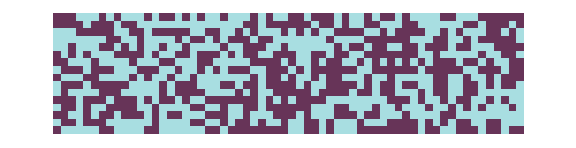

```mathematica
ArrayPlot[Partition[sequence,16]ᵀ,]
```

```mathematica
CUSUMMaxRandomnessTest[sequence,"TestStatistic"]
```

40

```mathematica
CUSUMMaxRandomnessTest[sequence,"PValue"]
```

0.411511

### Applications

Reject a non-random sequence:

```mathematica
subsequence=RandomInteger[{0,1},40];
```

```mathematica
sequence=Flatten@Table[subsequence,20];
```

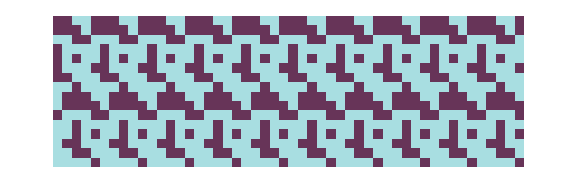

```mathematica
ArrayPlot[Partition[sequence,16]ᵀ,]
```

```mathematica
CUSUMMaxRandomnessTest[sequence,"TestStatistic"]
```

121

```mathematica
CUSUMMaxRandomnessTest[sequence,"PValue"]
```

0.0000754334

Test the randomness of rule 30:

```mathematica
rule30seq=CellularAutomaton[30, {{1}, 0}, {100000,0}]ᵀ⟦1⟧;
```

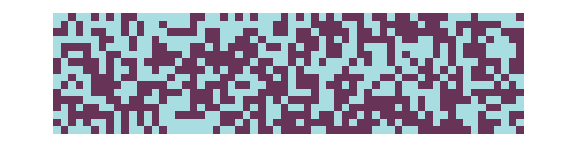

```mathematica
ArrayPlot[Partition[Take[rule30seq,1000],16]ᵀ,]
```

```mathematica
CUSUMMaxRandomnessTest[rule30seq]
```

0.740419

### Properties and Relations

### Possible Issues

CUSUMMaxRandomnessTest requires sequences of length 100 or more:

```mathematica
CUSUMMaxRandomnessTest[RandomInteger[{0,1},50]]
```

CUSUMMaxRandomnessTest::seqlength: The sequence length is less than 100 bits!

### Neat Examples

Visualize the sampling distribution of the test statistic:

```mathematica
samp=Table[CUSUMMaxRandomnessTest[RandomInteger[{0,1},1000],"TestStatistic"],1000];
```

```mathematica
Histogram[samp,Automatic,"PDF"]
```

-Graphics-

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

Emmy/Noah Blumenthal
noahb320@gmail.com
emmyb320@bu.edu

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

Randomness

Statistics

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

DistributionFitTest

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

OPERM5RandomnessTest

ChiSquareRandomnessTest

RunCountRandomnessTest

RunLengthRandomnessTest

BinaryRunRandomnessTest

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

N.I.S.T., A Statistical Test Suite for Random and Pseudorandom Number Generators for Cryptographic Applications, Special Publication 800-22, Revision 1a

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

NIST Report

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

## Author Notes

This test is entirely derived form the NIST publication.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

Additional information for the reviewer.